```mathematica
Quit[]
```

# One-Loop Vacuum Polarization in QED

For the differential equation and the boundary condition, please refer to https://arxiv.org/abs/0707.4037

#### Import the package and configure SeaSyde

```mathematica
SetDirectory[NotebookDirectory[]];
<<"../SeaSyde.m"
```

+++++ SeaSyde` +++++
Version 1.1.0

SeaSyde is a package for solving the system of differential equation associated to the Master Integrals of a given topology.

For any question or comment, please contact: 
[T. Armadillo](mailto:tommaso.armadillo@uclouvain.be), [R. Bonciani](mailto:roberto.bonciani@roma1.infn.it), [S. Devoto](mailto:simone.devoto@unimi.it), [N. Rana](mailto:narayan.rana@unimi.it) or [A. Vicini](mailto:alessandro.vicini@mi.infn.it).

For the latest version please see the [GitHub repository](https://github.com/TommasoArmadillo/SeaSyde).

It is possible to access the current configuration using

```mathematica
CurrentConfiguration[]
```

<|EpsilonOrder→2,ExpansionOrder→50,InternalWorkingPrecision→250,ChopPrecision→100,LogarithmicExpansion→False,RadiusOfConvergence→2,LogarithmicSingularities→{},SafeSingularities→{},Warning→True|>

and modify every parameter

```mathematica
Configuration={
EpsilonOrder->2,
ExpansionOrder->50
};
UpdateConfiguration[Configuration]
```

SeaSyde: Updated EpsilonOrder parameter, new value -> 2

SeaSyde: Updated ExpansionOrder parameter, new value -> 50

#### Prepare the package

Define the equation

```mathematica
MasterIntegral={B[x,ϵ]};
PointBC={0};
Equation={Derivative[1,0][B][x,ϵ]+1/2 (1/x-(1-2 ϵ)/(1+x)) B[x,ϵ]==(4^(-1+ϵ) π^ϵ (1/x-1/(1+x)) (1-ϵ) Gamma[1+ϵ])/(2-2 ϵ)};
BoundaryConditions= {B[0,ϵ]-((4π)^ϵ Gamma[1+ϵ])/4==0};
```

Note that B(x,ϵ) is related to J(x,ϵ) from the reference article through B(x,ϵ)=ϵJ(x,ϵ), so that the master is finite for ϵ→0. Although this is not necessary, it is something which is usually done. The explicit ϵ dependence in B(x,ϵ) might be omitted.

```mathematica
SetSystemOfDifferentialEquation[Equation,BoundaryConditions,MasterIntegral,{x-I δ},PointBC]
```

SeaSyde: There are 1 kinematics variables {x}

SeaSyde: The Feynman prescriptions for the variables are {-ⅈ δ}

SeaSyde: There are 1 Master Integrals

SeaSyde: The boundary conditions are imposed in x==0.

SeaSyde: The boundary conditions are given as precise value of the solution.

SeaSyde: There are 1 equations and 1 boundary conditions

SeaSyde: The possible singularities for the kinematics variables {x} are respectively {{-1.,0.}}

SeaSyde: The system of differential equation has been set and expanded in ϵ

Check that the equation has been correctly set

```mathematica
GetSystemOfDifferentialEquation[]//N
```

{0.5 (1/x-(1. (1.-2. ϵ))/(1.+x)) B[x]-(1. 3.14159^ϵ 4.^(-1.+ϵ) (1/x-1./(1.+x)) (1.-1. ϵ) Gamma[1.+ϵ])/(2.-2. ϵ)+B'[x]==0.,B[0.]-1. 3.14159^ϵ 4.^(-1.+ϵ) Gamma[1.+ϵ]==0.}

```mathematica
GetSystemOfDifferentialEquationExpanded[]//N
```

{{-0.125/(x (1.+x))+(0.5 B^0[x])/(1. x+x^2)+B^0'[x]==0.,-0.25+B^0[0.]==0.},{-0.244226/(x (1.+x))+(1. B^0[x])/(1.+x)+(0.5 B^1[x])/(1. x+x^2)+B^1'[x]==0.,-0.488452+B^1[0.]==0.},{-0.341394/(x (1.+x))+(1. B^1[x])/(1.+x)+(0.5 B^2[x])/(1. x+x^2)+B^2'[x]==0.,-0.682788+B^2[0.]==0.}}

It is possible to check wether the singularities of the equation have a logarithmic behaviour or not, that is if they are associated to a branch-cut. This step is very time consuming, especially for big systems of differential equations (30 eqs. or more). However, it is not necessary and it should be executed only if you are planning to make an intensive use of the TransportBoundaryConditions method, e.g. if you are going to construct a numerical grid which covers the entire phase-space. In this case it can save a lot of time in the transportation of the boundary conditions, because it may allows more direct paths between different points.

```mathematica
CheckSingularities[]
```

### Solve the system of differential equations

We can solve the system in the point where the boundary conditions are imposed (i.e. GetPoint[])

```mathematica
GetPoint[]//N
```

{x→0.}

```mathematica
SolveSystem[x]
```

Solving equation for ϵ order 0

Solving equation for ϵ order 1

Solving equation for ϵ order 2

I solved the system of equation. The error estimate is: 1.12636×10^-17.

We can access the complete solution with

```mathematica
Coefficient[Solution[][[1]],eps,1]//N
```

0.488452-0.166667 x+0.0666667 x^2-0.0380952 x^3+0.0253968 x^4-0.0184704 x^5+0.014208 x^6-0.0113664 x^7+0.00936057 x^8-0.00788259 x^9+0.0067565 x^10-0.00587522 x^11+0.00517019 x^12-0.00459573 x^13+0.00412031 x^14-0.00372157 x^15+0.00338324 x^16-0.00309325 x^17+0.00284245 x^18-0.0026238 x^19+0.00243181 x^20-0.00226215 x^21+0.00211134 x^22-0.00197657 x^23+0.00185556 x^24-0.00174641 x^25+0.00164756 x^26-0.00155769 x^27+0.00147571 x^28-0.00140067 x^29+0.00133178 x^30-0.00126837 x^31+0.00120983 x^32-0.00115565 x^33+0.00110541 x^34-0.0010587 x^35+0.00101519 x^36-0.000974586 x^37+0.000936615 x^38-0.000901047 x^39+0.000867675 x^40-0.000836313 x^41+0.000806796 x^42-0.000778976 x^43+0.000752718 x^44-0.000727903 x^45+0.000704422 x^46-0.000682178 x^47+0.000661079 x^48-0.000641047 x^49+0.000622006 x^50

or directly the numerical value in the centre of the series, in this case x=0.

```mathematica
SolutionValue[]//N
```

{0.25+0.488452 ϵ+0.682788 ϵ^2}

```mathematica
SolutionTable[]//N
```

{{0.25,0.488452,0.682788}}

Note that the coefficients of the solution are given with 250 digits (InternalWorkingPrecision parameter in the configuration).
We can plot the Master Integrals using

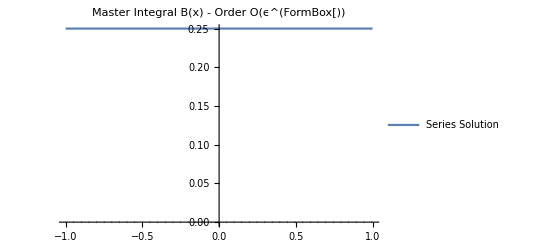

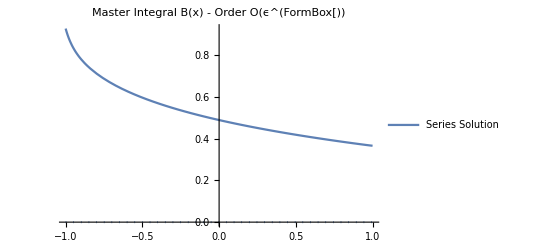

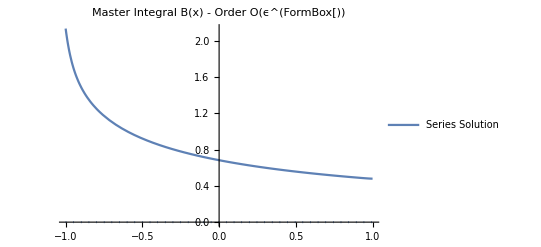

```mathematica
CreateGraph[1,0,-1,1]
CreateGraph[1,1,-1,1]
CreateGraph[1,2,-1,1]
```

The physical region, in terms of the kinematic variable x, is x≤0. At the moment the radius of convergence of the solution is limited by the presence of the singularity x=-1. To obtain a solution which is valid also for x≤-1, e.g. in x=-2, we can use TransportBoundaryConditions. SeaSyde automatically performs the analytic continuation.

SeaSyde: Moving following these points: {0.,0.-0.5 ⅈ,-2.-0.5 ⅈ,-2.}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable x

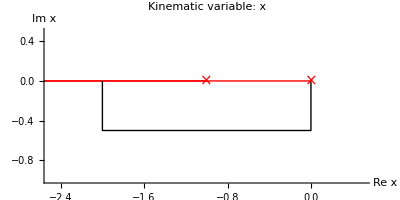

SeaSyde: Moving from the point x=0. to x=0.-0.5 ⅈ, along the line x=(0.-0.5 ⅈ) tInt

SeaSyde: The new point is: x=0.-0.5 ⅈ

SeaSyde: Moving from the point x=0.-0.5 ⅈ to x=-2.-0.5 ⅈ, along the line x=(0.-0.5 ⅈ)-2. tInt

SeaSyde: The new point is: x=-0.25-0.5 ⅈ

SeaSyde: The new point is: x=-0.529508-0.5 ⅈ

SeaSyde: The new point is: x=-0.872788-0.5 ⅈ

SeaSyde: The new point is: x=-1.13075-0.5 ⅈ

SeaSyde: The new point is: x=-1.38916-0.5 ⅈ

SeaSyde: The new point is: x=-1.70596-0.5 ⅈ

SeaSyde: Moving from the point x=-2.-0.5 ⅈ to x=-2., along the line x=(-2.-0.5 ⅈ)+(0.+0.5 ⅈ) tInt

SeaSyde: I arrived at x=-2.. The error estimate is: 2.96667×10^-17.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

```mathematica
TransportVariable[x,-2]
```

Note that now the boundary conditions are imposed in x=-2. When TransportBoundaryConditions will be called again SeaSyde will start moving from x=-2.
The series now converges in x∈(-3,-1). Note that nor in the previous case, nor in this one, we expect the solution to be accurate around x=-1. If we would like to obtain a precise solution around x=-1 we should the equation at x=-1.

SeaSyde: Moving following these points: {-2.,-1.}, avoiding singularities. Here you can see the path in the complex plane for the kinematic variable x

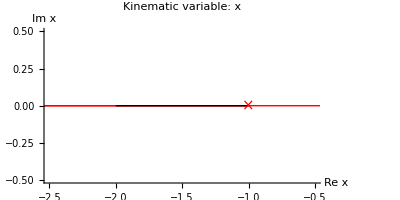

SeaSyde: Moving from the point x=-2. to x=-1., along the line x=-2.+1. tInt

SeaSyde: The new point is: x=-1.5

SeaSyde: I arrived at x=-1.. The error estimate is: 2.96667×10^-17.
Use Solution[] or SolutionValue[] to access the solution, or CreteGraph to plot it.

```mathematica
TransportVariable[x,-1]
```

Now the solution converges in x∈(-2,0). We can compare the solution we obtained with the exact one for the order O(ϵ^1) of B(x,ϵ), that we recall is the finite order for J(x,ϵ). The exact solution has been obtained using the built-in Mathematica function DSolve.

```mathematica
ExactSolution[x_]:=1/(4 √x)(2 √x-EulerGamma √x-2 √(1+x) ArcSinh[√x]+√x Log[4 π]);
```

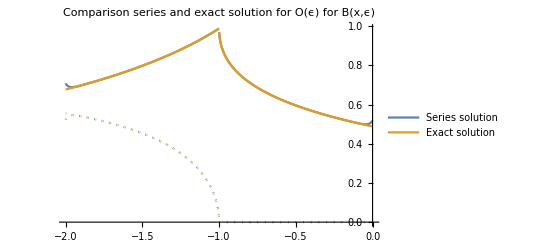

```mathematica
ReImPlot[{Coefficient[Solution[][[1]], ϵ, 1], ExactSolution[x-1*^-20 I]},{x,-2,0},PlotLabel->"Comparison series and exact solution for O(ϵ) for B(x,ϵ)",PlotLegends->{{"Series solution", "Exact solution"},"ReIm"}]
```

The two solutions perfectly overlap.